## Name: Vimal Joshi Rol no:20201430 COURSE= Bsc (H) COMPUTER SCIENCE practical-2 Secant method

## Secant Method:Taking parameter as input

x0 = 1

x1 = 2

Nmax = 20

epsilon = 1/1000000

f[x] := Cos[x]

In1th Numer of iteration the root is:1.5649

Estimated error is : 0.435096

In2th Numer of iteration the root is:1.57098

Estimated error is : 0.0060742

In3th Numer of iteration the root is:1.5708

Estimated error is : 0.000182249

Return[1.5708]

Root is:1.5708

Estimated error is : 1.02185×10^-9

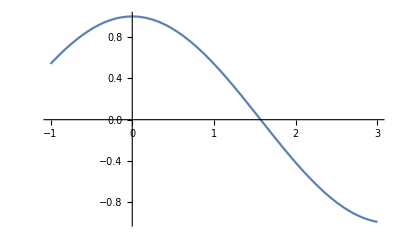

```mathematica
x0 = Input["Enter first guess :"];
x1 = Input["Enter second guess :"];
Nmax =Input["Enter maximum number of iterations :"];
eps = Input["Enter a value of convergence parameter :"];
Print["x0 = ",x0];
Print["x1 = ",x1];
Print["Nmax = ",Nmax];
Print["epsilon = ",eps];
f[x_] := Cos[x];
Print["f[x] := ",f[x]];
For[i = 1,i≤Nmax,i++,
x2=N[x1-(f[x]/.x->x1)*(x1-x0)/((f[x]/.x->x1)-(f[x]/.x->x0))];
If[Abs[x1-x2]<eps,Return[x2],x0=x1;x1=x2];
Print["In",i,"th Numer of iteration the root is:",x2];
Print["Estimated error is : ",Abs[x1-x0]]];
Print["Root is:",x2];
Print["Estimated error is : ",Abs[x2-x1]];
Plot[f[x],{x,-1,3}]
```

x0 = 0

x1 = 1

Nmax = 20

epsilon = 1/1000000

f[x] := Cos[x]

In1th Numer of iteration the root is:2.17534

Estimated error is : 1.17534

In2th Numer of iteration the root is:1.57278

Estimated error is : 0.602559

In3th Numer of iteration the root is:1.57067

Estimated error is : 0.00211435

In4th Numer of iteration the root is:1.5708

Estimated error is : 0.000126873

Return[1.5708]

Root is:1.5708

Estimated error is : 7.81941×10^-11

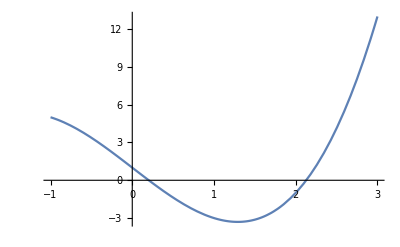

```mathematica
x0 = Input["Enter first guess :"];
x1 = Input["Enter second guess :"];
Nmax =Input["Enter maximum number of iterations :"];
eps = Input["Enter a value of convergence parameter :"];
Print["x0 = ",x0];
Print["x1 = ",x1];
Print["Nmax = ",Nmax];
Print["epsilon = ",eps];
f[x_] :=x^3 -5*x+1;
Print["f[x] := ",f[x]];
For[i = 1,i≤Nmax,i++,
x2=N[x1-(f[x]/.x->x1)*(x1-x0)/((f[x]/.x->x1)-(f[x]/.x->x0))];
If[Abs[x1-x2]<eps,Return[x2],x0=x1;x1=x2];
Print["In",i,"th Numer of iteration the root is:",x2];
Print["Estimated error is : ",Abs[x1-x0]]];
Print["Root is:",x2];
Print["Estimated error is : ",Abs[x2-x1]];
Plot[f[x],{x,-1,3}]
```

x0 = 0

x1 = 1

Nmax = 20

epsilon = 1/1000000

f[x] := Cos[x]

In1th Numer of iteration the root is:2.17534

Estimated error is : 1.17534

In2th Numer of iteration the root is:1.57278

Estimated error is : 0.602559

In3th Numer of iteration the root is:1.57067

Estimated error is : 0.00211435

In4th Numer of iteration the root is:1.5708

Estimated error is : 0.000126873

Return[1.5708]

Root is:1.5708

Estimated error is : 7.81941×10^-11

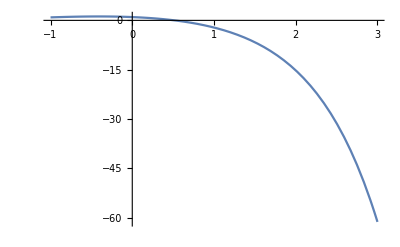

```mathematica
x0 = Input["Enter first guess :"];
x1 = Input["Enter second guess :"];
Nmax =Input["Enter maximum number of iterations :"];
eps = Input["Enter a value of convergence parameter :"];
Print["x0 = ",x0];
Print["x1 = ",x1];
Print["Nmax = ",Nmax];
Print["epsilon = ",eps];
f[x_] :=Cos[x]-x*Exp[x];
Print["f[x] := ",f[x]];
For[i = 1,i≤Nmax,i++,
x2=N[x1-(f[x]/.x->x1)*(x1-x0)/((f[x]/.x->x1)-(f[x]/.x->x0))];
If[Abs[x1-x2]<eps,Return[x2],x0=x1;x1=x2];
Print["In",i,"th Numer of iteration the root is:",x2];
Print["Estimated error is : ",Abs[x1-x0]]];
Print["Root is:",x2];
Print["Estimated error is : ",Abs[x2-x1]];
Plot[f[x],{x,-1,3}]
```